```mathematica
IQSphere[q_,R_]:=((4/3*Pi*R^3)*3*(Sin[q*R]-q*R*Cos[q*R])/(q*R)^3)^2
```

```mathematica
Integrate[q*BesselJ[0,q*z]*IQSphere[q,R],{q,0,Infinity},Assumptions->z>0 && z<2*R]
```

Integrate[(16 π^2 BesselJ[0,q z] (-q R Cos[q R]+Sin[q R])^2)/q^5,{q,0,∞},Assumptions→z>0&&z<2 R]

```mathematica
gamma[r_,R_]:=1-3/4*r/R+1/16*(r/R)^3
```

```mathematica
1/Integrate[gamma[r,R],{r,0,2*R}]*Integrate[gamma[r,R]*r/Sqrt[r^2-z^2],{r,z,2*R}, Assumptions->z>0&&z<2*R]
```

(6 R √(4 R^2-z^2) (8 R^2+z^2)+(48 R^2 z^2-3 z^4) Log[z/(2 R+√(4 R^2-z^2))])/(96 R^4)

```mathematica
FullSimplify[(6 R √(4 R^2-z^2) (8 R^2+z^2)+(48 R^2 z^2-3 z^4) Log[z/(2 R+√(4 R^2-z^2))])/(96 R^4),Assumptions->R>0&&z>0]
```

(6 R √(4 R^2-z^2) (8 R^2+z^2)+(48 R^2 z^2-3 z^4) Log[z/(2 R+√(4 R^2-z^2))])/(96 R^4)

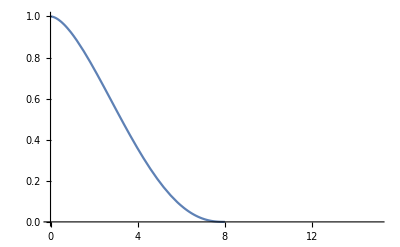

```mathematica
Plot[ReplaceAll[(6 R √(4 R^2-z^2) (8 R^2+z^2)+(48 R^2 z^2-3 z^4) Log[z/(2 R+√(4 R^2-z^2))])/(96 R^4),R->4],{z,0.001,15}]
```

```mathematica
FullSimplify[ReplaceAll[(6 R √(4 R^2-z^2) (8 R^2+z^2)+(48 R^2 z^2-3 z^4) Log[z/(2 R+√(4 R^2-z^2))])/(96 R^4),z->xi*2*R],Assumptions->x>0&&R>0]
```

1/2 (√(1-xi^2) (2+xi^2)-xi^2 (-4+xi^2) Log[xi/(1+√(1-xi^2))])